```mathematica
Simulate Brownian motion and geometric Brownian motion sample path
By Le Chen.
Crated on Wed 17 Nov 2021 09:14:01 AM CST
```

```mathematica
Simulate the standard Brownian path
```

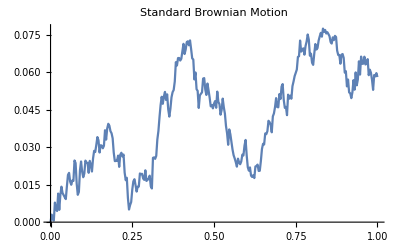

```mathematica
n=300; (* This is the number of steps in t ∈ [0,1] *)
p = RandomVariate[NormalDistribution[0,1/n],n]; (* Generate independent Brownian increments *)
f={{0,0}};(* Brownian motion starts from (0,0) *)
For[i=0,i<n,i++;f=Append[f, {i/n,p[[i]]+f[[i]][[2]]}]]; (* Add all increments to form Brownian path. *)
ListLinePlot[f,PlotLabel->"Standard Brownian Motion"] (* Plot the Brownian path. *)
```

```mathematica
Simulate the geometric Brownian motion
```

```mathematica
d Subscript[S, t] = μ Subscript[S, t] dt + σ Subscript[S, t] d Subscript[W, t]
Subscript[S, t] = Subscript[S, 0] ⅇ^((μ-σ^2/2)t + σ Subscript[W, t])
```

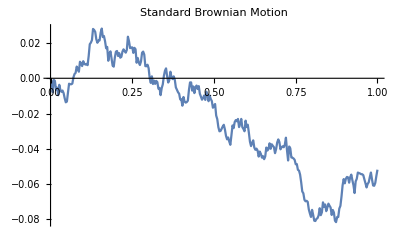

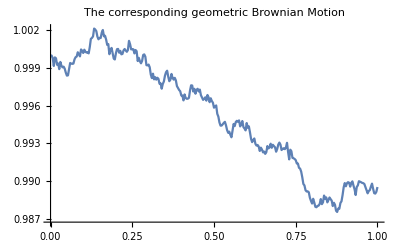

```mathematica
(* Setting parameters *)
μ=0; 
σ = 0.1;
Subscript[S, 0]=1;
(* We first generate the Brownian path. *)
n=300; (* This is the number of steps in t ∈ [0,1] *)
p = RandomVariate[NormalDistribution[0,1/n],n]; (* Generate independent Brownian increments *)
f={{0,0}};(* Brownian motion starts from (0,0) *)
For[i=0,i<n,i++;f=Append[f, {i/n,p[[i]]+f[[i]][[2]]}]] 
(* Mow we can form the corresponding geometric Brownian path. *)
g ={{0,Subscript[S, 0]}};(* Geometric Brownian motion starts from (0,Subscript[S, 0]) *)
For[i=0,i<n,i++;g=Append[g, {i/n,Subscript[S, 0] Exp[(μ-σ^2/2)i/n+σ f[[i]][[2]]]}]]; 
(* Now we can plot two paths. *)
ListLinePlot[{f},PlotRange->Full,PlotLabel->"Standard Brownian Motion"]
ListLinePlot[{g},PlotRange->Full,PlotLabel->"The corresponding geometric Brownian Motion"](* Plot the Brownian path. *)
```